# Derivation of scattering from a solid sphere.

```mathematica
$Assumptions:={R>0, q>0,r>0,Sin[θq]>= 0,θq> 0,θq<= π/2}
```

We start by looking at a sphere, which is the easiest solid body to work with given its symmetry . Any scatterer within the solid sphere can be expressed with a spherical coordinate:

```mathematica
Rvec:={r Cos[θ]Sin[ϕ],r Sin[θ]Sin[ϕ],r Cos[ϕ]}
```

Here ϕ is the angle  Rvec makes with the z axis and θ is the angle the xy projection makes with the x axis. The measure with this choice of coordinates is r^2 dθ dCos[ϕ]

We can place the q vecor along any direction due to rotational symmetry, easiest direction is z

```mathematica
qvec={0,0,q}
```

{0,0,q}

```mathematica
Rvec.qvec
```

q r Cos[ϕ]

Some useful normalization constants : surface of the unit sphere, and radial factor for calculating the volume of a sphere:

```mathematica
Integrate[ Sin[θ],{θ,0,π},{ϕ,-π,π}]
```

4 π

```mathematica
Integrate[ r^2,{r,0,R}]
```

R^3/3

To get the form factor amplitude relative to the centre of the sphere, we integrate the interference contribution from all scatterers on a spherical surface at r:

```mathematica
Ashell=Integrate[Exp[I q r Cosθ ]/(4 π), {Cosθ ,-1,1},{ϕ,-π,π}]
```

Sin[q r]/(q r)

Which is well known from the Debye formula. To get a the form factor amplitude of a sphere, we have an additional integral over r in [0:R] taking the measure 4π r^2 and normalization volume  (4π R.b3/3) into account:

```mathematica
Aspherecenter=Integrate[Ashell r^2/(R^3/3),{r,0,R}]
```

(3 (-q R Cos[q R]+Sin[q R]))/(q^3 R^3)

Which is the form factor amplitude relative to the centre of the sphere . Any pair distance between two scatterers can be stated as the convolution of two vectors connecting a scatterer to the origin . Fourier transforming the pair distance turns it into products of the Fourier transforms . Hence the form factor is just the form factor amplitude squared :

```mathematica
Fsphere=Aspherecenter^2
```

(9 (-q R Cos[q R]+Sin[q R])^2)/(q^6 R^6)

Reference  to form factor of sphere: L . Rayleigh, Proc . R . Soc ., London . A84, 25 (1911) .

Radius of gyration of a sphere :

```mathematica
Solve[Normal[Series[Fsphere,{q,0,3}]]==1-(Rg2 q^2)/3,Rg2]
```

{{Rg2→(3 R^2)/5}}

MSD beween random points inside a sphere . (sigma = 2)

```mathematica
Solve[Normal[Series[Fsphere,{q,0,3}]]==1-(σR2 q^2)/6,σR2]
```

{{σR2→(6 R^2)/5}}

MSD from the centre to any scatterer in the sphere  (sigma=1):

```mathematica
Solve[Normal[Series[Aspherecenter,{q,0,3}]]==1-(σR2 q^2)/6,σR2]
```

{{σR2→(3 R^2)/5}}

Since the sphere was derived from integrating radial shells, we can also inverse this calculation and rederive the form factor amplitude of the shell by differentiating wrt . R when proper volume and area measures are taken into account .

```mathematica
D[(4π R^3)/3 Aspherecenter,R]/(4π R^2)//Simplify
```

Sin[q R]/(q R)

The form factor of a spherical shell is

```mathematica
Fshell=Ashell^2
```

Sin[q r]^2/(q^2 r^2)

MSD from a random site on the surface to another random site on the surface (sigma=2)

```mathematica
Solve[Normal[Series[Fshell,{q,0,3}]]==1-(Rg2 q^2)/3,Rg2]
```

{{Rg2→r^2}}

```mathematica
Solve[Normal[Series[Fshell,{q,0,3}]]==1-(σR2 q^2)/6,σR2]
```

{{σR2→2 r^2}}

By construction same result as for Rg2=R2 since sigma=2.

MSD from center to surface . For a sphere this is R by definition . NB  sigma = 1.

```mathematica
Solve[Normal[Series[Ashell,{q,0,3}]]==1-(σR2 q^2)/6,σR2]
```

{{σR2→r^2}}

The form factor amplitude of a sphere relative to a random point on the surface, is the convolution of  a step from the surface to the centre and from the centre to a site inside this sphere:

```mathematica
Asphereshell=Ashell Aspherecenter/.r->R
```

(3 Sin[q R] (-q R Cos[q R]+Sin[q R]))/(q^4 R^4)

MSD from random point on surface to random point inside the sphere  (sigma=1):

```mathematica
Solve[Normal[Series[Asphereshell,{q,0,3}]]==1-(σR2 q^2)/6,σR2]
```

{{σR2→(8 R^2)/5}}

#### Comparing to sampled data and saving data for validation:

```mathematica
Clear[PARENTDIR,DIR1,DIRO1]
```

```mathematica
PARENTDIR=Directory[]
```

/home/zqex/source/SEB/Mathematica

```mathematica
DIR1:=PARENTDIR<>"/Sampled/SolidSphericalShell_Ri2.33_Ro3.44/"
DIRO1:=PARENTDIR<>"/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/"
CreateDirectory[DIRO1];
```

CreateDirectory::eexist: /home/zqex/source/SEB/Examples/Validation/SolidSphere_R1/ already exists.

```mathematica
SaveFunction[func_,filename_,NN_,qmin_,qmax_]:=Module[{},Export[filename,{#,N[func[#]]}&/@Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]]]
SetAttributes[SaveFunction,HoldAll]
```

```mathematica
Clear[qvec,qq]
```

```mathematica
qvec[qmin_,qmax_,NN_]:=Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]
qq:=qvec[0.8,50,500]//N
```

#### Form factor :

(9 (-q R Cos[q R]+Sin[q R])^2)/(q^6 R^6)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphere_R1/F.dat

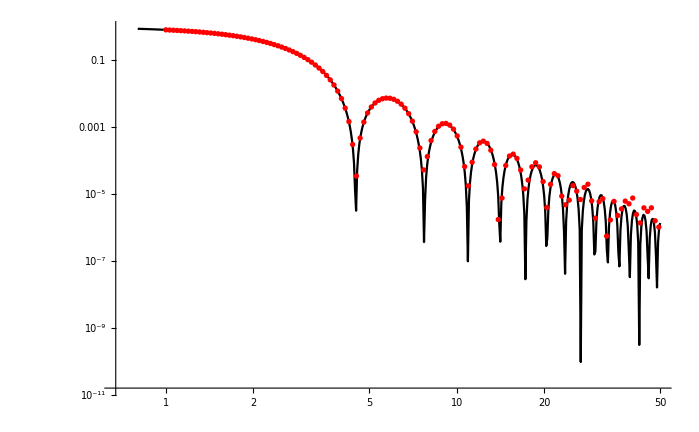

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Fsphere
Func1[q_]:=Term[q]/.R-> 1
FILE="FF.q";
OFILE=DIRO1<>"F.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Form factor amplitude (center) :

(3 (-q R Cos[q R]+Sin[q R]))/(q^3 R^3)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphere_R1/FFA_center.dat

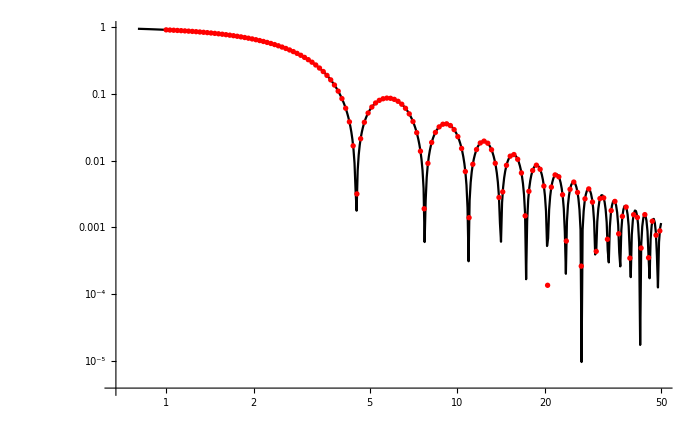

```mathematica
Clear[Term,Func1,DATA,FILE,OFILE]
Term[q_]=Aspherecenter
Func1[q_]:=Term[q]/.R-> 1
FILE="FFA_center.q";
OFILE=DIRO1<>"FFA_center.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Form factor amplitude relative to surface:

(3 Sin[q R] (-q R Cos[q R]+Sin[q R]))/(q^4 R^4)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphere_R1/FFA_surface.dat

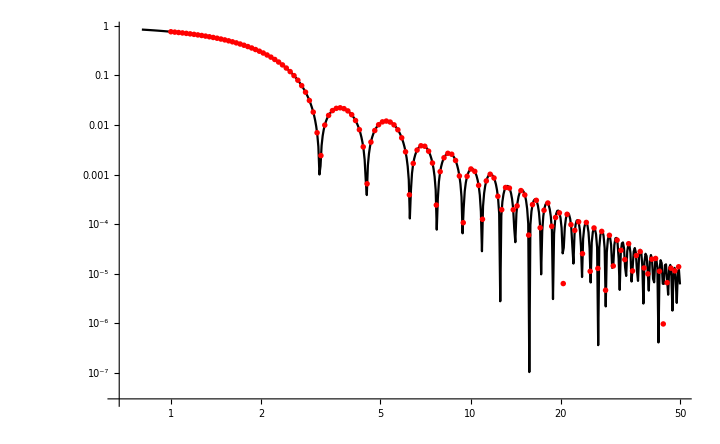

```mathematica
Clear[Term,Func1,DATA,FILE,OFILE]
Term[q_]=Asphereshell
Func1[q_]:=Term[q]/.R-> 1
FILE="FFA_surface.q";
OFILE=DIRO1<>"FFA_surface.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor relative to center-to-surface:

Sin[q r]/(q r)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphere_R1/PF_center_surface.dat

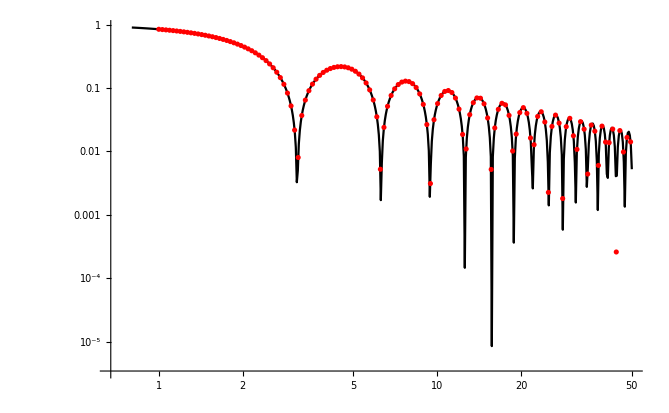

```mathematica
Clear[Term,Func1,DATA,FILE,OFILE]
Term[q_]=Ashell
Func1[q_]:=Term[q]/.r-> 1
FILE="PF_center_surface.q";
OFILE=DIRO1<>"PF_center_surface.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor surface-to-surface:

Sin[q r]^2/(q^2 r^2)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphere_R1/PF_surface_surface.dat

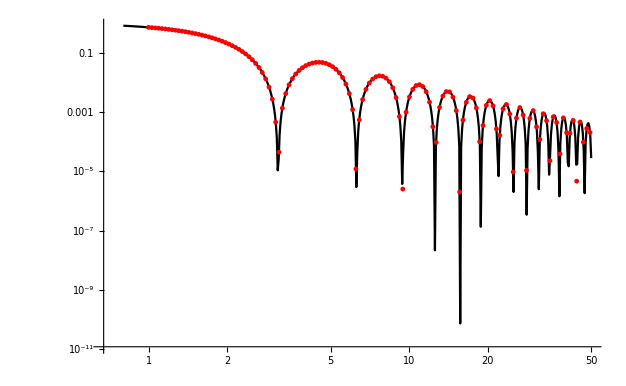

```mathematica
Clear[Term,Func1,DATA,FILE,OFILE]
Term[q_]=Fshell
Func1[q_]:=Term[q]/.r-> 1
FILE="PF_surface_surface.q";
OFILE=DIRO1<>"PF_surface_surface.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```